```mathematica
Clear[n,d,L,ϕ]
```

```mathematica
(*Steady state*)
```

```mathematica
Pst[x_]:=1/(2L)
```

```mathematica
FullSimplify[Integrate[Pst[x],{x,-L,L},Assumptions->{d>0,L>0}]]
```

1

```mathematica
(*General solution*)
```

```mathematica
DSolve[d*ϕ''[x]==-λ*ϕ[x],ϕ[x],x]
```

{{ϕ[x]→C[1] Cos[(x √λ)/(√d)]+C[2] Sin[(x √λ)/(√d)]}}

```mathematica
(*Solutions*)
```

```mathematica
ϕ[x_]:=(c1*Cos[((√λ)/(√d))x] +c2*Sin[((√λ)/(√d))x] )
```

```mathematica
(*Definition of the probability current*)
```

```mathematica
J[x_]:=d*ϕ'[x]
```

```mathematica
(*Periodic boundary conditions*)
```

```mathematica
eq1=FullSimplify[ϕ[L]-ϕ[-L]]
eq2=FullSimplify[J[L]-J[-L]]
```

2 c2 Sin[(L √λ)/(√d)]

-2 c1 √d √λ Sin[(L √λ)/(√d)]

```mathematica
(*Coefficient matrix of the linear system*)
```

```mathematica
M=(({{0, 0}, {0, 0}}));
M[[1]][[1]]=FullSimplify[eq1/.{c1->1,c2->0}];
M[[1]][[2]]=FullSimplify[eq1/.{c1->0,c2->1}];
M[[2]][[1]]=FullSimplify[eq2/.{c1->1,c2->0}];
M[[2]][[2]]=FullSimplify[eq2/.{c1->0,c2->1}];
MatrixForm[M]
```

(0 | 2 Sin[(L √λ)/(√d)]
-2 √d √λ Sin[(L √λ)/(√d)] | 0)

```mathematica
FullSimplify[Det[M]]
```

4 √d √λ Sin[(L √λ)/(√d)]^2

```mathematica
(*We have a null eigenvalue and the rest given by the eq. Cos[(L √λ)/(√d)]=1*)
```

```mathematica
FullSimplify[Solve[(L √λ)/(√d)==n*π,λ]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{λ→(d n^2 π^2)/L^2}}

```mathematica
(*The eigenvalues are degenerate; there are two eigenfunctions per eigenvalue, with c1 and c2 being free parameters*)
```

```mathematica
(*We find two eigenfunctions by setting either c1 or c2 to 0 *)
```

```mathematica
ϕ1n[x_]:=FullSimplify[(ϕ[x]/.{λ->(d n^2 π^2)/L^2})]/.c2->0
ϕ2n[x_]:=FullSimplify[(ϕ[x]/.{λ->(d n^2 π^2)/L^2})]/.c1->0
```

```mathematica
FullSimplify[ϕ1n[x],Assumptions->{d>0,n>0,L>0,Mod[n,1]==0}]
FullSimplify[ϕ2n[x],Assumptions->{d>0,n>0,L>0,Mod[n,1]==0}]
```

c1 Cos[(n π x)/L]

c2 Sin[(n π x)/L]

```mathematica
(*We uniquely determine the first eigenfunction by normalizing it*)
```

```mathematica
Integrate[(ϕ1n[x])^2/Pst[x],{x,-L,L},Assumptions->{d>0,L>0,Mod[n,1]==0}]
```

2 c1^2 L^2

```mathematica
solc4=FullSimplify[Solve[2 c1^2 L^2==1,c1]]
```

{{c1→-1/(√2 L)},{c1→1/(√2 L)}}

```mathematica
ϕ1f[x_]:=FullSimplify[ϕ1n[x]/.solc4[[2]]]
```

```mathematica
FullSimplify[ϕ1f[x],Assumptions->{d>0,n>0,L>0,Mod[n,1]==0}]
```

Cos[(n π x)/L]/(√2 L)

```mathematica
(*Same for the second one*)
```

```mathematica
Integrate[(ϕ2n[x])^2/Pst[x],{x,-L,L},Assumptions->{d>0,L>0,Mod[n,1]==0}]
```

2 c2^2 L^2

```mathematica
solc3=FullSimplify[Solve[2 c2^2 L^2==1,c2],Assumptions->{d>0,L>0,n>0}]
```

{{c2→-1/(√2 L)},{c2→1/(√2 L)}}

```mathematica
ϕ2f[x_]:=FullSimplify[ϕ2n[x]/.solc3[[2]]]
```

```mathematica
FullSimplify[ϕ2f[x],Assumptions->{d>0,n>0,L>0,Mod[n,1]==0}]
```

Sin[(n π x)/L]/(√2 L)

```mathematica
(*Checking orthogonality*)
```

```mathematica
Integrate[((ϕ1f[x])(ϕ2f[x]))/Pst[x],{x,-L,L},Assumptions->{d>0,L>0,Mod[n,1]==0}]
```

0

```mathematica
(*Plot the eigenfunctions*)
```

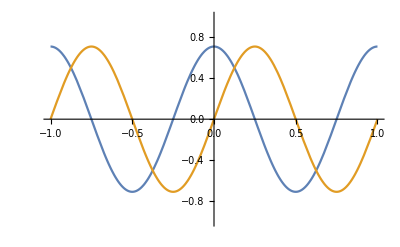

```mathematica
n=2;
d=1;
L=1;
Show[Plot[{ϕ1f[x],ϕ2f[x]},{x,-L,L}],PlotRange->{{-L,L},{-1,1}}]
```

```mathematica
(*Computing the transition probabilities*)
```

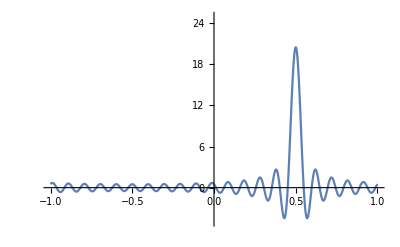

```mathematica
c1v[x0_]:=ϕ1f[x0]/Pst[x0]
c2v[x0_]:=ϕ2f[x0]/Pst[x0]
d=1;
L=1;
x0=0.5;
ncut=20;
Plot[Pst[x]+Sum[c1v[x0]*ϕ1f[x],{n,1,ncut}]+Sum[c2v[x0]*ϕ2f[x],{n,1,ncut}],{x,-L,L},PlotRange->{{-L,L},{-5,25}}]
```